```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

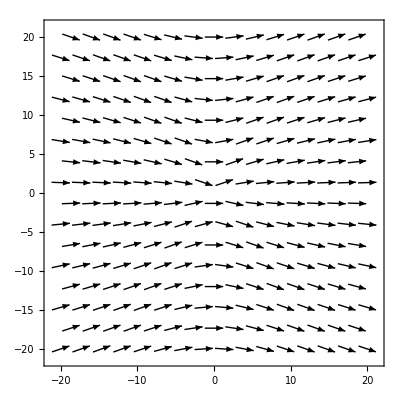

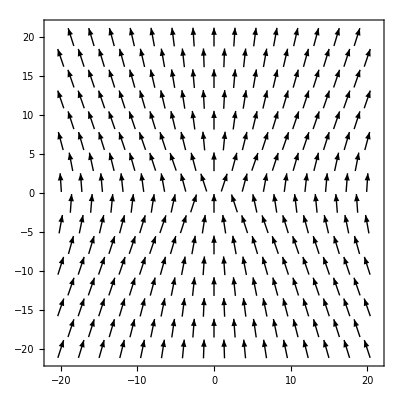

```mathematica
VectorPlot[g1[x,y],{x,-20,20},{y,-20,20}]
VectorPlot[g2[x,y],{x,-20,20},{y,-20,20}]
```

```mathematica
y0:={100,100}
```

```mathematica
y0hat:=y0/Norm[y0];
```

```mathematica
epsilon:=1/Norm[y0]
```

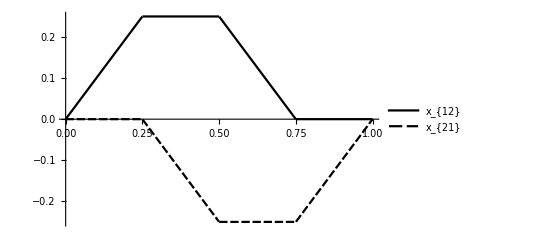

```mathematica
x1[t_]:={0,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx1[t_]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
Plot[{x1[t][[2]],x2[t][[1]]},{t,0,1},PlotLegends->LineLegend[{"x_{12}","x_{21}"},LegendFunction->Frame]]
```

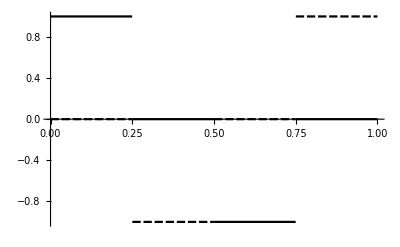

```mathematica
Plot[{dx1[t][[2]],dx2[t][[1]]},{t,0,1}]
```

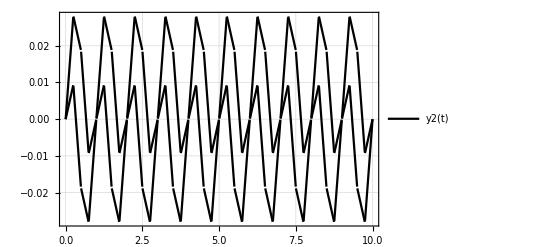

```mathematica
y2[t_]=G2[y0hat].x1[t]+ G2[y0hat].x2[t];
Plot[y2[t],{t,0,10},PlotTheme->"Detailed"]
y22=NDSolveValue[{y'[t]==(3/40)(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
y23=NDSolveValue[{y'[t]==(3/40)(y2[t] y0hat.dx1[t]+y2[t] y0hat.dx2[t]+y0hat y2[t].(dx1[t]+dx2[t])-(dx1[t]+dx2[t])(y0hat.y2[t])-3(y2[t].y0hat)(y0hat.(dx1[t]+dx2[t])y0hat)),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

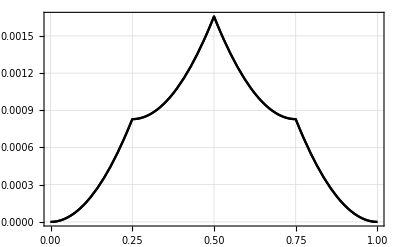

```mathematica
Plot[y22[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{22}(t)"]
```

```mathematica
x11[t_?NumericQ]:={0,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx11[t_?NumericQ]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
y3=NDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]==y0},b,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

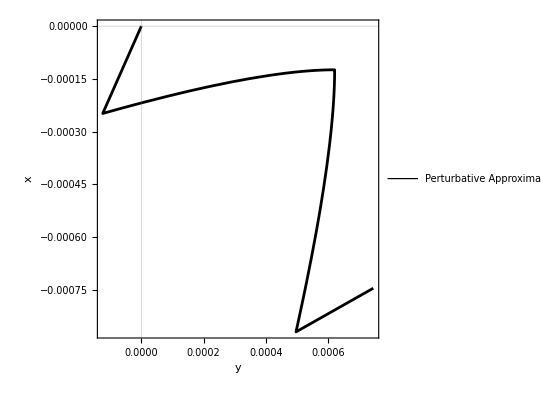

```mathematica
ParametricPlot[{y23[t]},{t,0,1},AspectRatio->1, FrameLabel->{"y","x"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotLegends->LineLegend[{"Perturbative Approximation"},LegendFunction->Frame],PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

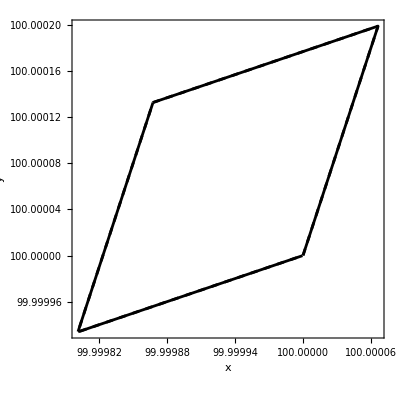

```mathematica
curve=ParametricPlot[{y0+epsilon y2[t]+epsilon^2 y22[t],y3[t]},{t,0,1},AspectRatio->1, FrameLabel->{"x","y"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

```mathematica
dd1 =epsilon^2(y22[1.0]-y22[0])
y2[1]-y2[0]
dd2=y3[1]-y3[0]
dd3=epsilon^3(y23[1]-y23[0])
displ[h_]:=1/(Norm[h]^6)(27/2560)(0.1){h[[2]]^3+h[[2]]h[[1]]^2,-h[[1]]^3-h[[1]]h[[2]]^2}
dd4=N[displ[y0]]
Norm[dd4-dd3]
```

{9.94369×10^-22,9.94369×10^-22}

{0,0}

{2.648×10^-10,-2.632×10^-10}

{2.636718749999985×10^-10,-2.636718750000017×10^-10}

{2.63672×10^-10,-2.63672×10^-10}

2.23265×10^-24

```mathematica
curve2=ParametricPlot[{x1[t],x2[t]},{t,0,1}];
```

```mathematica
Animate[{Show[curve2,Graphics[{PointSize[Large],Point[x1[t]],Point[x2[t]]}]],Show[curve,Graphics[{PointSize[Large],Point[y0+epsilon y2[t]+epsilon^2 y22[t]]}]]},{t,0,1},RefreshRate->30];
y4=ParametricNDSolveValue[{b'[t] == G2[b[t] - x11[t]].dx11[t] + G2[b[t] - x21[t]].dx21[t], b[0] == {a,c}}, b[1]-b[0], {t, 0, 1},{a,c}, Method -> "StiffnessSwitching",  WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25]
```

ParametricFunction[<>]

```mathematica
y5=ParametricNDSolveValue[{y'[t]==(3/40)epsilon^2(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={a,c}},y[1]-y[0],{t,0,1},{a,c},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

```mathematica
y21[t_,a_,b_]:=G[a,b].(x1[t]+x2[t]);
y6=Integrate[(3/4)(y21[t,q,p] {q,p}.dx1[t]+y21[t,q,p] {q,p}.dx2[t]+{q,p} y21[t,q,p] .(dx1[t]+dx2[t])-(dx1[t]+dx2[t])({q,p}.y21[t,q,p] )-3(y21[t,q,p] .{q,p})({q,p}.(dx1[t]+dx2[t]){q,p})),{t,0,1}]
```

{(27 (p^3+p q^2))/(2560 (p^2+q^2)^(3/2)),-(27 (p^2 q+q^3))/(2560 (p^2+q^2)^(3/2))}

```mathematica
Block[{$PerformanceGoal="Speed"},{LogLogPlot[{y4[p,0].{1,0},p^(-8/2)},{p,1,10},PlotTheme->"Scientific",PlotPoints->10]}]
```

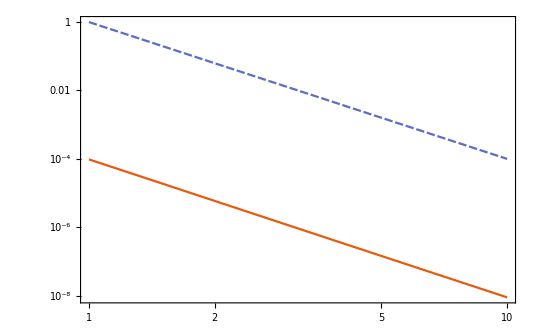

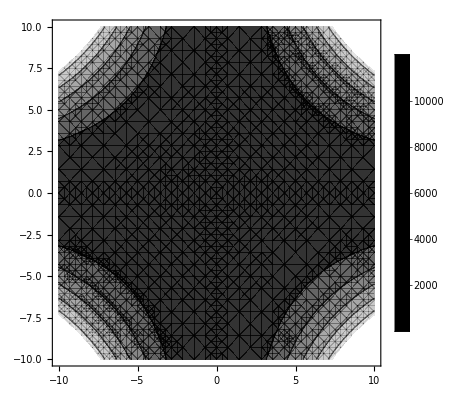

```mathematica
ContourPlot[p^2 q^2+p^2 q^2,{p,-10,10},{q,-10,10},PlotTheme->"Detailed"]
```

```mathematica
displacement1[{q_,p_}] := (27/25600)(p^2+q^2)^(-6/2) {p^3+p q^2,-p^2q - q^3}
```

```mathematica
Block[{$PerformanceGoal="Speed"},{LogLogPlot[{Norm[displacement1[{p,0}]-y4[p,0]],p^(-2),10^(-25)},{p,10^(-2),10^9},FrameLabel->{"r","Error(r)"},PlotTheme->"Scientific",PlotLegends->LineLegend[{"Computed Error in Displacement","ϵ^4","Machine Precision"},LegendFunction->Frame],PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]},{Dashed, Black,Thickness[0.0025]}},PlotPoints->10,WorkingPrecision->25]}]
```

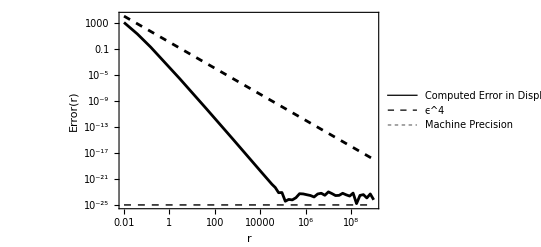

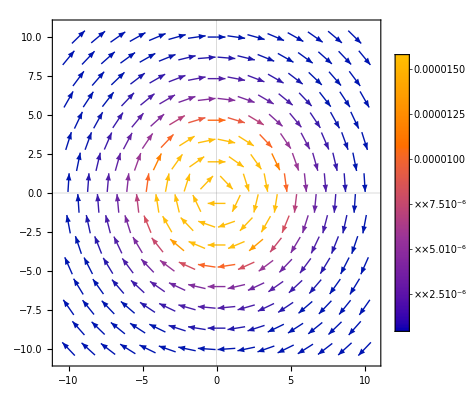

```mathematica
VectorPlot[displacement1[{q,p}],{q,-10,10},{p,-10,10},PlotLegends->Automatic,PlotTheme->"Scientific"]
```